```mathematica
Z[x_] = -(2/(a*T))^(1/2)*ArcSin[(1-x)^(1/2)]
```

-√2 √(1/(a T)) ArcSin[√(1-x)]

```mathematica
a = 1/2; T = 2;
```

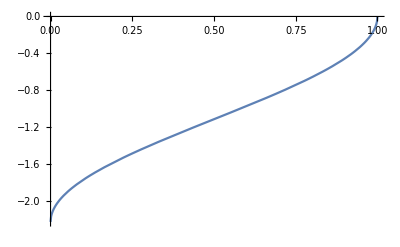

/Users/caballrm/Dropbox (Personal)/Probabilistic_Wind_Power_Forecasting/Mathematica_Files/Range_Z.pdf

```mathematica
RangeZ = Plot[Z[x],{x,0,1},PlotPoints->10]
Export[NotebookDirectory[]<>"Range_Z.pdf",RangeZ]
```

```mathematica
Z[0]
```

-π/(√2)

```mathematica
Z[1]
```

0